```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/morning_sec_int_data/368nm.dat"]
```

{{1.12389,-0.628484},{1.13423,-0.612028},{1.14739,-0.623752},{1.16401,-0.634312},{1.183,-0.638545},{1.20042,-0.657413},{1.22646,-0.673403},{1.24828,-0.673501},{1.27782,-0.689992},{1.30453,-0.716273},{1.34407,-0.73324},{1.38078,-0.761041},{1.41705,-0.786118},{1.46132,-0.832432},{1.51023,-0.862703},{1.58758,-0.916616},{1.63065,-0.938869}}

0.127876-0.651365 x

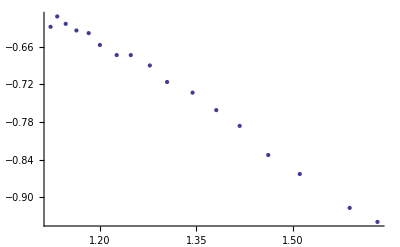

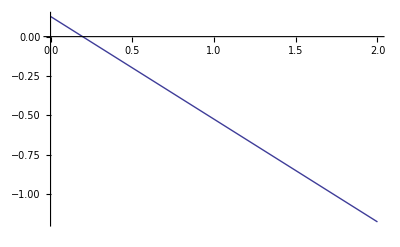

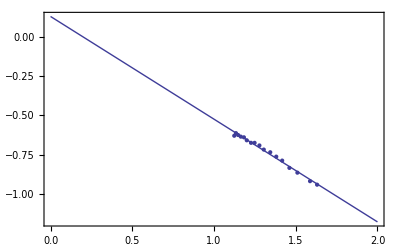

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```